## Study of the deformed potential with quadrupole character of a single-particle j moving in a field generated by the triaxial rotor R

```mathematica
ClearAll["Global`*"]
```

### Constants

```mathematica
A=163;
β=0.38;
j=13/2;
γ=20;
```

```mathematica
rad[degs_]:=degs*π/180;
```

The Spherical Harmonics Y_lm(θ,φ)

```mathematica
YLM[l_,m_]:=SphericalHarmonicY[l,m,θ,φ];
```

The coupling constant C=195/(j(j+1))A^(-1/3)β_2 and the coupling factor from the potential V(β_2,γ)

```mathematica
Cpl[A_,β_,j_]:=195/(j(j+1))A^(-1/3)*β;
CplV[A_,β_]:=206/A^(1/3)*β;
c=CplV[A,β];
```

```mathematica
Vsp[A_,β_,γ_]:=CplV[A,β]*(Cos[γ]*YLM[2,0]+Sin[γ]/Sqrt[2](YLM[2,2]+YLM[2,-2]));
```

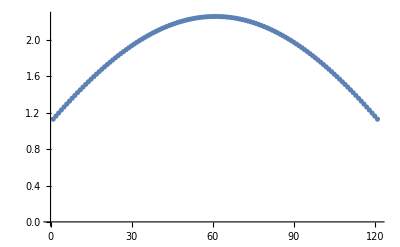

```mathematica
ListPlot[Table[Vsp[A,β,rad[x]]/.{θ->π/4,φ->π/4},{x,-60,60,1}]]
```

## Function for making a grid of plots

```mathematica
makeGrid[contourList_]:=Grid[{Table[Show[contourList[[i]]],{i,1,Length[contourList]/2}],Table[Show[contourList[[i]]],{i,Length[contourList]/2+1,Length[contourList]}]},Frame->All];
(*makeGrid[{c1,c1,c1,c1}]*)
```

## Function for generating a single contour plot with the single-particle deformed potential

### Parameters for the contour are β,γ

```mathematica
makeContour[β_,γ_]:=ContourPlot[Vsp[A,β,rad[γ]],{θ,0,π},{φ,0,2π},FrameStyle->Directive[Black,Thick],AspectRatio->1,ColorFunction->"BlueGreenYellow",Frame->True,FrameLabel->{"θ [rad]","φ [rad]"},LabelStyle->{18,FontFamily->"Times",Bold,Black},Contours->Automatic,ContourStyle->{Black,Opacity[1]},(*ContourLabels->(Style[Text[#3,{#1,#2}],Red,Bold,17,FontFamily->"Times"]&),*)PlotLegends->Automatic,ImageSize->Medium,PlotRange->Full,PlotLabel->Style[StringTemplate["Single-particle potential V_sp\nj=π(i_(13/2))  β=``  γ=(``)^0"][β,γ],15,Black,Italic,Plain]];
```

## Study the β-variation of the single-particle potential

```mathematica
c1=makeContour[0.1,20];
c2=makeContour[0.15,20];
c3=makeContour[0.25,20];
c4=makeContour[0.38,20];
contoursc={c1,c2,c3,c4};
fig1=makeGrid[contoursc];
save["plot1",fig1];
```

## Function for exporting a graphics object into a custom location

```mathematica
save[file_,object_]:=Export[StringTemplate["/Users/robertpoenaru/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DevWorkspace/Github/physics-code-collection/Code-Collection/Quadrupole-Deformed-MeanField/``.pdf"][file],object,ImageResolution->1200];
```

## Study the β-variation of the single-particle potential

```mathematica
d1=makeContour[0.30,-30];
d2=makeContour[0.30,10];
d3=makeContour[0.30,45];
d4=makeContour[0.30,60];
contoursd={d1,d2,d3,d4};
fig2=makeGrid[contoursd];
save["plot2",fig2]
```

/Users/robertpoenaru/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DevWorkspace/Github/physics-code-collection/Code-Collection/Quadrupole-Deformed-MeanField/plot2.pdf

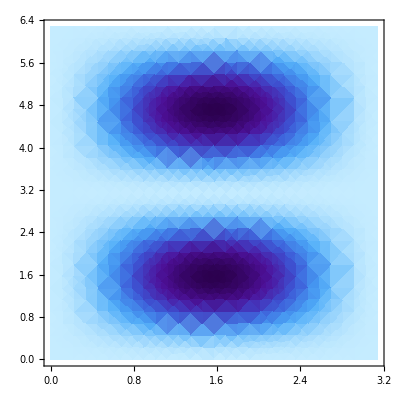

```mathematica
CoolColor[ z_ ] :=RGBColor[z,1-z,1];DensityPlot[Vsp[A,0.30,rad[60]],{θ,0,π},{φ,0,2π},ColorFunction->"DeepSeaColors"(*MeshFunctions->{#3&},Mesh->{Range[-3,3]},MeshStyle->{Black, Thin}*)]
```

## Graphical representation of the spherical harmonics for the triaxial potential -Graphics-

```mathematica
SphericalPlot3D[Re[SphericalHarmonicY[2,-2,θ,φ]]+Re[SphericalHarmonicY[2,2,θ,φ]]+SphericalHarmonicY[2,0,θ,φ],{θ,0,π},{φ,0,2π}]
```

-Graphics3D-